```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*below select the proper file name corresponding to the existing pddf file, found in the path given by SetDirectory[NotebookDirectory[]] command*)
```

```mathematica
data=Import["pddf_alpha-curve_tot_100%.dat"];
```

InterpolatingFunction::dmval: Input value {0.00301502} lies outside the range of data in the interpolating function. Extrapolation will be used.

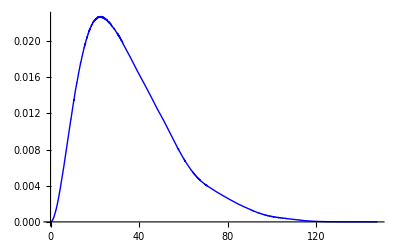

```mathematica
datainterp=Interpolation[data,InterpolationOrder->0];plotinterp=Plot[datainterp[r],{r,Min[data],Max[data]},PlotStyle->{Blue,Thick}]
```

```mathematica
Rg=(NIntegrate[r^2 datainterp[r],{r,0,120}]/2)^(1/2)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {79.6856}. NIntegrate obtained 1673.19 and 0.53527 for the integral and error estimates.

28.9239

```mathematica
(*correction for RG of RBD+Sb23 complex is about 4%*)
```

```mathematica
Rgfin=(Rg+0.04 Rg)^1
```

30.0809

```mathematica
Max[Select[data,#[[2]]>10^-4&]⟦;;,1⟧]
```

116.741